```mathematica
ClearAll["Global`*"]
```

```mathematica
K[n_] := If[ n==1,0,FullSimplify[MangoldtLambda[n]/Log[n]]]
ST[n_]:= Mod[n,vv=3]-Mod[(n-1),vv]
LAdd[n_] := Sum[ vv^k/k,{k,1,Log[vv,n]}]
E1[n_,0]:=1
E1[n_,k_] := E1[n,k] = Sum[ ST[j] E1[Floor[n/j],k-1],{j,1,n}]
E2[n_,k_] := E2[n,k] = Sum[ (-1)^(k-j) Binomial[k,j] E1[n,j],{j,0,k}]
P2[n_] := Sum[ (-1)^(k+1)/k E2[n,k],{k,1,Log[2,n]}]
M2[n_] := Sum[ (-1)^(k) E2[n,k],{k,0,Log[2,n]}]
Mert[n_] := Sum[ MoebiusMu[j],{j,1,n}]
MertAdd[n_, v_] := Sum[ -Mert[Floor[n/v^j]]*v^j,{j,1,Log[v,n]}]
```

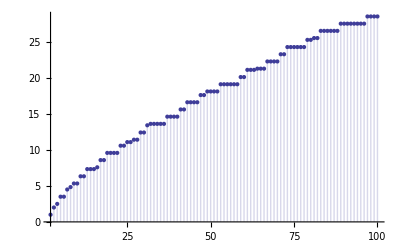

```mathematica
DiscretePlot[P2[n]+LAdd[n],{n,2,100}]
```

```mathematica
Table[ {n, P2[n]-P2[n-1],(P2[n]-P2[n-1]-K[n])},{n,2,100}]//TableForm
```

2 | -1 | -2
3 | 1 | 0
4 | -3/2 | -2
5 | 1 | 0
6 | 0 | 0
7 | 1 | 0
8 | -7/3 | -8/3
9 | 1/2 | 0
10 | 0 | 0
11 | 1 | 0
12 | 0 | 0
13 | 1 | 0
14 | 0 | 0
15 | 0 | 0
16 | -15/4 | -4
17 | 1 | 0
18 | 0 | 0
19 | 1 | 0
20 | 0 | 0
21 | 0 | 0
22 | 0 | 0
23 | 1 | 0
24 | 0 | 0
25 | 1/2 | 0
26 | 0 | 0
27 | 1/3 | 0
28 | 0 | 0
29 | 1 | 0
30 | 0 | 0
31 | 1 | 0
32 | -31/5 | -32/5
33 | 0 | 0
34 | 0 | 0
35 | 0 | 0
36 | 0 | 0
37 | 1 | 0
38 | 0 | 0
39 | 0 | 0
40 | 0 | 0
41 | 1 | 0
42 | 0 | 0
43 | 1 | 0
44 | 0 | 0
45 | 0 | 0
46 | 0 | 0
47 | 1 | 0
48 | 0 | 0
49 | 1/2 | 0
50 | 0 | 0
51 | 0 | 0
52 | 0 | 0
53 | 1 | 0
54 | 0 | 0
55 | 0 | 0
56 | 0 | 0
57 | 0 | 0
58 | 0 | 0
59 | 1 | 0
60 | 0 | 0
61 | 1 | 0
62 | 0 | 0
63 | 0 | 0
64 | -21/2 | -32/3
65 | 0 | 0
66 | 0 | 0
67 | 1 | 0
68 | 0 | 0
69 | 0 | 0
70 | 0 | 0
71 | 1 | 0
72 | 0 | 0
73 | 1 | 0
74 | 0 | 0
75 | 0 | 0
76 | 0 | 0
77 | 0 | 0
78 | 0 | 0
79 | 1 | 0
80 | 0 | 0
81 | 1/4 | 0
82 | 0 | 0
83 | 1 | 0
84 | 0 | 0
85 | 0 | 0
86 | 0 | 0
87 | 0 | 0
88 | 0 | 0
89 | 1 | 0
90 | 0 | 0
91 | 0 | 0
92 | 0 | 0
93 | 0 | 0
94 | 0 | 0
95 | 0 | 0
96 | 0 | 0
97 | 1 | 0
98 | 0 | 0
99 | 0 | 0
100 | 0 | 0

```mathematica
ST2[n_, k_]:= Mod[n,k]-Mod[(n-1),k]
```

```mathematica
Table[ {n,ST2[n,11/10]},{n,2,40}]//TableForm
```

2 | -1/10
3 | -1/10
4 | -1/10
5 | -1/10
6 | -1/10
7 | -1/10
8 | -1/10
9 | -1/10
10 | -1/10
11 | -1/10
12 | 1
13 | -1/10
14 | -1/10
15 | -1/10
16 | -1/10
17 | -1/10
18 | -1/10
19 | -1/10
20 | -1/10
21 | -1/10
22 | -1/10
23 | 1
24 | -1/10
25 | -1/10
26 | -1/10
27 | -1/10
28 | -1/10
29 | -1/10
30 | -1/10
31 | -1/10
32 | -1/10
33 | -1/10
34 | 1
35 | -1/10
36 | -1/10
37 | -1/10
38 | -1/10
39 | -1/10
40 | -1/10

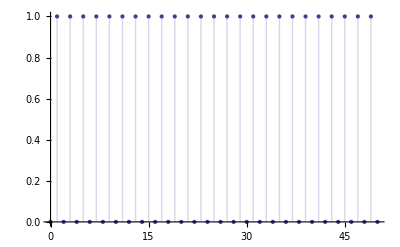

```mathematica
DiscretePlot[ E1[n,1],{n,0,50}]
```

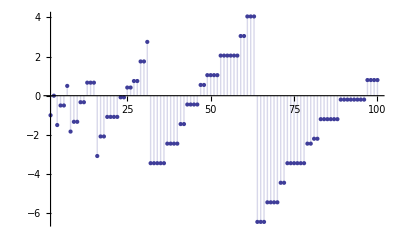

```mathematica
DiscretePlot[P2[n],{n,2,100}]
```

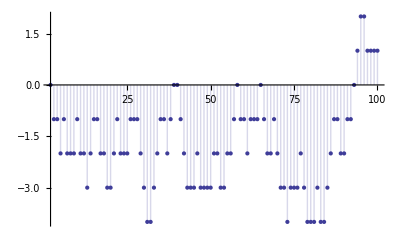

```mathematica
DiscretePlot[M2[n]+MertAdd[n,vv],{n,2,100}]
```

```mathematica
Table[{n,M2[n]+MertAdd[n,vv], Mert[n]},{n,1,100}]//TableForm
```

1 | 1 | 1
2 | 0 | 0
3 | -1 | -1
4 | -1 | -1
5 | -2 | -2
6 | -1 | -1
7 | -2 | -2
8 | -2 | -2
9 | -2 | -2
10 | -1 | -1
11 | -2 | -2
12 | -2 | -2
13 | -3 | -3
14 | -2 | -2
15 | -1 | -1
16 | -1 | -1
17 | -2 | -2
18 | -2 | -2
19 | -3 | -3
20 | -3 | -3
21 | -2 | -2
22 | -1 | -1
23 | -2 | -2
24 | -2 | -2
25 | -2 | -2
26 | -1 | -1
27 | -1 | -1
28 | -1 | -1
29 | -2 | -2
30 | -3 | -3
31 | -4 | -4
32 | -4 | -4
33 | -3 | -3
34 | -2 | -2
35 | -1 | -1
36 | -1 | -1
37 | -2 | -2
38 | -1 | -1
39 | 0 | 0
40 | 0 | 0
41 | -1 | -1
42 | -2 | -2
43 | -3 | -3
44 | -3 | -3
45 | -3 | -3
46 | -2 | -2
47 | -3 | -3
48 | -3 | -3
49 | -3 | -3
50 | -3 | -3
51 | -2 | -2
52 | -2 | -2
53 | -3 | -3
54 | -3 | -3
55 | -2 | -2
56 | -2 | -2
57 | -1 | -1
58 | 0 | 0
59 | -1 | -1
60 | -1 | -1
61 | -2 | -2
62 | -1 | -1
63 | -1 | -1
64 | -1 | -1
65 | 0 | 0
66 | -1 | -1
67 | -2 | -2
68 | -2 | -2
69 | -1 | -1
70 | -2 | -2
71 | -3 | -3
72 | -3 | -3
73 | -4 | -4
74 | -3 | -3
75 | -3 | -3
76 | -3 | -3
77 | -2 | -2
78 | -3 | -3
79 | -4 | -4
80 | -4 | -4
81 | -4 | -4
82 | -3 | -3
83 | -4 | -4
84 | -4 | -4
85 | -3 | -3
86 | -2 | -2
87 | -1 | -1
88 | -1 | -1
89 | -2 | -2
90 | -2 | -2
91 | -1 | -1
92 | -1 | -1
93 | 0 | 0
94 | 1 | 1
95 | 2 | 2
96 | 2 | 2
97 | 1 | 1
98 | 1 | 1
99 | 1 | 1
100 | 1 | 1

```mathematica
f[n_,k_] := Mod[n,k]-Mod[n-1,k]
```

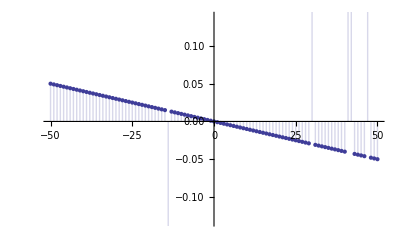

```mathematica
DiscretePlot[f[222343,(1+k/1000)],{k,-50,50}]
```